```mathematica
ContractGame[g_]:=Block[{mpgs,formula,neigh,gBis,result={},found={},matches,count=1},
mpgs=Map[SortEdge,CollectMPGEdges[g]];
Table[
With[{contract=EdgeContract[g,e,GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]},
matches=Select[found,IsomorphicGraphQ[contract,#[[1]]]&];
If[matches≠{},
AppendTo[result,e->Reverse[First [matches]]]
,
{{AppendTo[found,{contract,count}];
AppendTo[result,e->{count,contract}];}, {count++;}}
]
],
{e,mpgs}
];
result
]
```

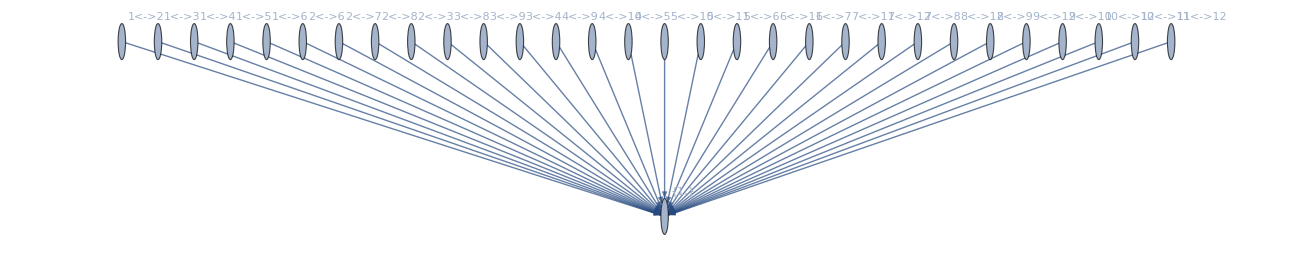

```mathematica
Graph[ContractGame[Graph[plantri[[1]]]],VertexLabels->"Name"]
```

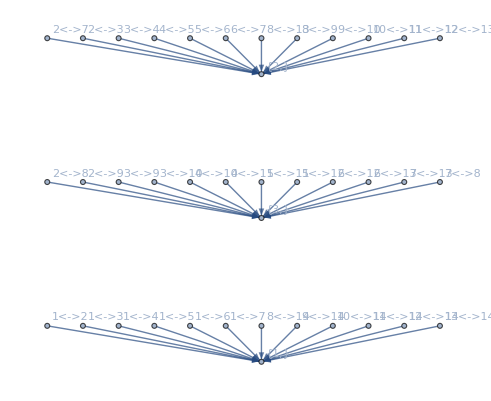

```mathematica
Graph[ContractGame[Graph[plantri[[2]]]],VertexLabels->"Name"]
```

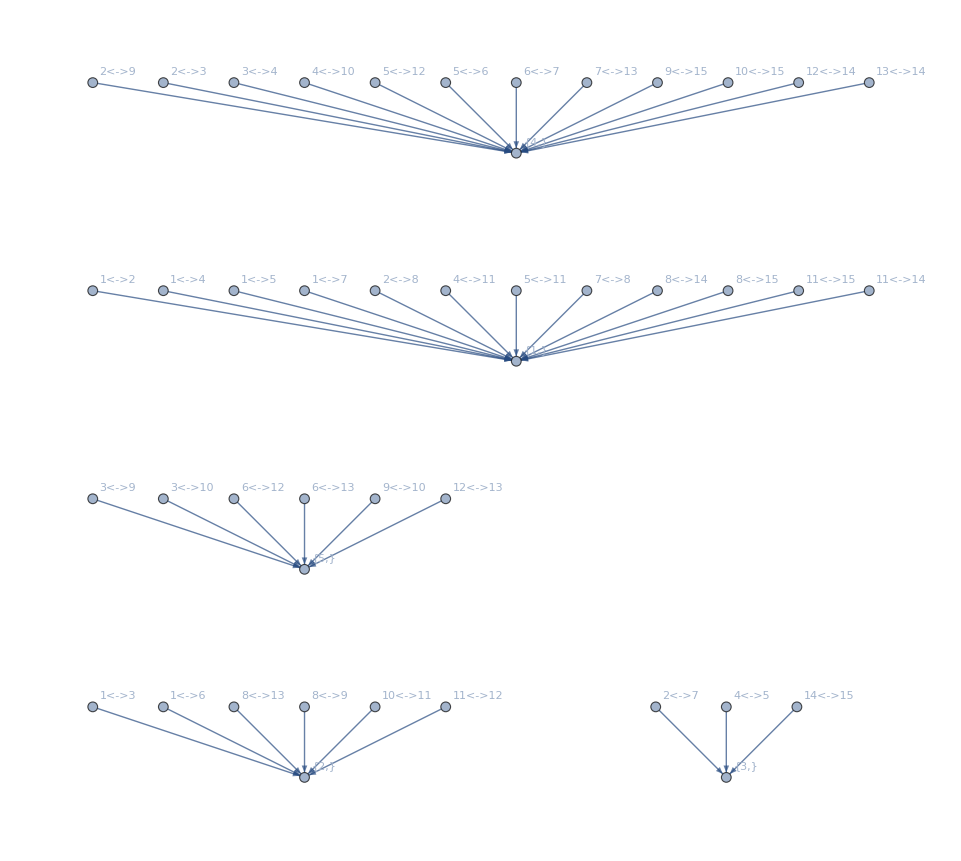

```mathematica
Graph[ContractGame[Graph[plantri[[3]]]],VertexLabels->"Name"]
```

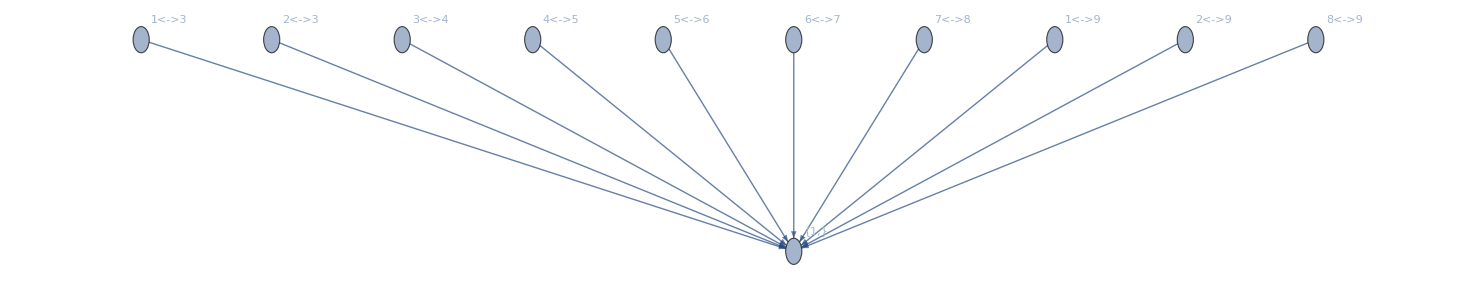

```mathematica
Graph[ContractGame[MinimalGraph[8]],VertexLabels->"Name"]
```

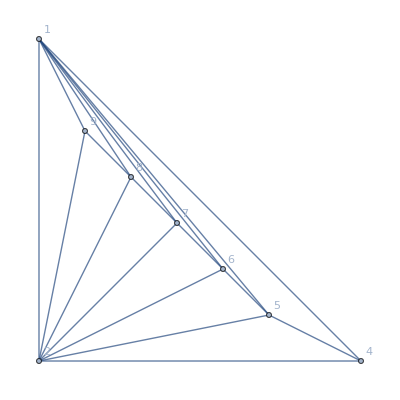
{1<->3→{1,-Graphics-},2<->3→{1,-Graphics-},3<->4→{1,-Graphics-},4<->5→{1,-Graphics-},5<->6→{1,-Graphics-},6<->7→{1,-Graphics-},7<->8→{1,-Graphics-},1<->9→{1,-Graphics-},2<->9→{1,-Graphics-},8<->9→{1,-Graphics-}}

```mathematica
ContractGame[MinimalGraph[8]]
```